```mathematica
Coupled Rate Equations for Lossy System w/ vib states
Last plots are scattered photons as function of laser powers
```

0.00263433

0.212652

0.101784

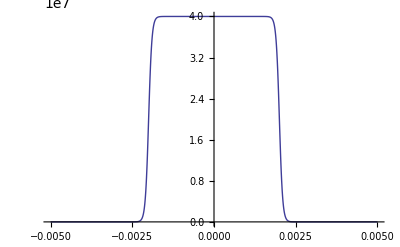

```mathematica
L=0.002; (*probe laser radius*)
d=.0001;(*probe laser intensity drop off at edges*)
c=299792458;(*speed of light*)
h=6.62607004*10^(-34);(*planck's constant*)
Z00=.9639;(*0.9639branching ratios from Lane PRA 2015*)
r00=0.96390;(*2Z00/3effective branching ratio to initial spin-rotation state*)
x00=r00/1;(*space saving quantity*)
r01=0.03590;(*0.0359effective branching ratio to initial spin-rotation state*)
x01=r01/1;(*space saving quantity*)
r02=0.00017;(*branching ratio 0-2*)
r12=0.07390;(*0.0359effective branching ratio to initial spin-rotation state*)
x12=r12/1;(*space saving quantity*)
r11=0.8169;
r10=0.11370;
r03=0.00003;(*losses to dark states*)
r13=0.00071;(*losses to dark states*)
λ=905*10^-9;(*probe wavelength*)
λ01=1009*10^-9;(*0-1probe wavelength*)
λ12=1014*10^-9;(*0-1probe wavelength*)
Γ=10*10^6;(*scattering rate*)
Δg12=2*Pi*15*10^6;(*ground state hyperfine splitting*)
Δg32=2*Pi*31*10^6;(*ground state hyperfine splitting*)
Δe=2*Pi*50*10^6;(*upper state hyperfine splitting (unknown!!!)*)
v=100;(*velocity of moleuclar beam*)
ini=-0.005;(*initial position to start the model*)
intini=-0.0049;(*initial position to start the integral*)
Isat=4*Pi*h*c*Γ/(λ^3*r00/3);(*classically defined saturation intensity*)
Isat01=4*Pi*h*c*Γ/(λ01^3*r01);(*classically defined saturation intensity*)
Isat12=4*Pi*h*c*Γ/(λ12^3*r12);(*classically defined saturation intensity*)
I0=8*Isat;(*probe laser intensity*)
I01=4.0*Isat01;(*probe laser intensity*)
I12=4.0*Isat12;(*probe laser intensity*)
s32=0;(*0 or one depending on if j=3/2 spin state is addressed*)
s12=1;(*0 or one depending on if j=1/2 spin state is addressed*)
ns=12;(*number of starting hyperfine states*)
power00=I0*Pi*0.001^2
power01=I01*Pi*0.005^2
power12=I12*Pi*0.005^2
δ=0*10^6;(*probe laser detuning*)
R[δ_,z_]:=((Γ/2)/(1+4δ^2/Γ^2))*((I0*(Tanh[z/d+L/d]-Tanh[z/d-L/d])/(2Tanh[L/d]))/Isat);(* excitation rate00*)
R01[δ_,z_]:=((Γ/2)/(1+4δ^2/Γ^2))*((I01*(Tanh[z/d+L/d]-Tanh[z/d-L/d])/(2Tanh[L/d]))/Isat01);(* excitation rate01*)
R12[δ_,z_]:=((Γ/2)/(1+4δ^2/Γ^2))*((I12*(Tanh[z/d+L/d]-Tanh[z/d-L/d])/(2Tanh[L/d]))/Isat12);(* excitation rate01*)
Plot[R[δ,z],{z,ini,-ini},PlotRange->All]
```

## Branching Ratios:

```mathematica
BR={{0,1/9,1/9,1/9},{1/9,1/9,1/9,0},{1/9,1/9,0,1/9},{1/9,0,1/9,1/9},{2/9,1/18,1/18,0},{2/9,1/18,0,1/18},{2/9,0,1/18,1/18},{0,1/3,0,0},{0,1/6,1/6,0},{0,1/18,2/9,1/18},{0,0,1/6,1/6},{0,0,0,1/3}};
```

```mathematica
Rate Equations
```

So here, I've taken into account the ground rotational state of the first 2 vibrational levels. Branching ratios are unique to B-X!!!

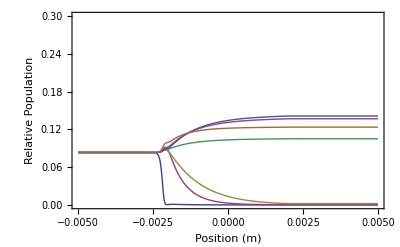

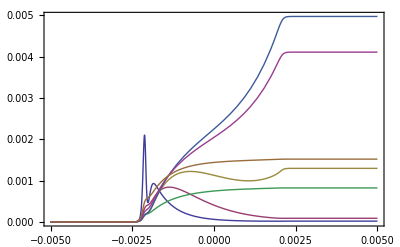

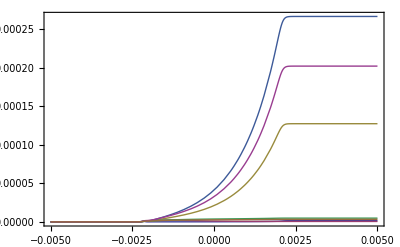

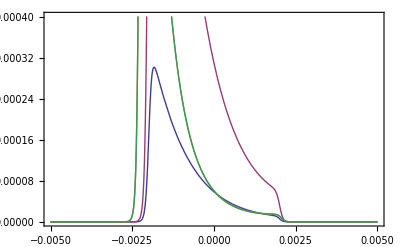

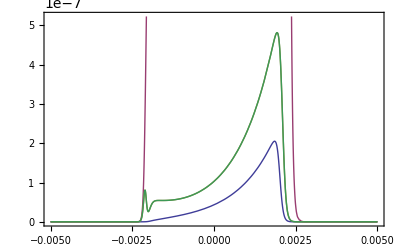

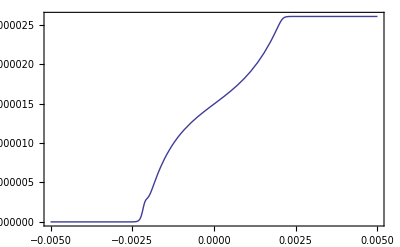

```mathematica
sol=NDSolve[
{v*Ng0'[z]==s12*R[δ,z]*(Ne2a[z]+Ne2b[z]-2Ng0[z])+(x00)*Γ*(BR[[1]][[3]]*Ne1[z]+BR[[1]][[2]]Ne2a[z]+BR[[1]][[4]]Ne2b[z])+(r10)*Γ*(BR[[1]][[3]]v1Ne1[z]+BR[[1]][[2]]v1Ne2a[z]+BR[[1]][[4]]v1Ne2b[z]),
v*Ng1'[z]==s12*R[δ+Δg12,z]*(Ne2a[z]+Ne2b[z]-2Ng1[z])+(x00)*Γ*(BR[[3]][[1]]*Ne0[z]+BR[[3]][[2]]Ne2a[z]+BR[[3]][[4]]Ne2b[z])+(r10)*Γ*(BR[[3]][[1]]v1Ne0[z]+BR[[3]][[2]]v1Ne2a[z]+BR[[3]][[4]]v1Ne2b[z]),v*Ng2a'[z]==s12*R[δ+Δg12,z]*(Ne1[z]-Ng2a[z])+s12*R[δ+Δg12-Δe,z]*(Ne0[z]-Ng2a[z])+(x00)*Γ*(BR[[2]][[1]]Ne0[z]+BR[[2]][[3]]Ne1[z]+BR[[2]][[2]]Ne2a[z])+(r10)*Γ*(BR[[2]][[1]]v1Ne0[z]+BR[[2]][[3]]v1Ne1[z]+BR[[2]][[2]]v1Ne2a[z]),v*Ng2b'[z]==s12*R[δ+Δg12,z]*(Ne1[z]-Ng2b[z])+s12*R[δ+Δg12-Δe,z]*(Ne0[z]-Ng2b[z])+(x00)*Γ*(BR[[4]][[1]]Ne0[z]+BR[[4]][[3]]Ne1[z]+BR[[4]][[4]]Ne2b[z])+(r10)*Γ*(BR[[4]][[1]]v1Ne0[z]+BR[[4]][[3]]v1Ne1[z]+BR[[4]][[4]]v1Ne2b[z]),

v*jNg0'[z]==s32*R[δ+Δg32,z]*(Ne2a[z]+Ne2b[z]-2*jNg0[z])+(x00)*Γ*(BR[[6]][[1]]Ne0[z]+BR[[6]][[2]]Ne2a[z]+BR[[6]][[4]]Ne2b[z])+(r10)*Γ*(BR[[6]][[1]]v1Ne0[z]+BR[[6]][[2]]v1Ne2a[z]+BR[[6]][[4]]v1Ne2b[z]),v*jNg0a'[z]==s32*R[δ+Δg32,z]*(Ne1[z]-jNg0a[z])+s32*R[δ+Δg32-Δe,z]*(Ne0[z]-jNg0a[z])+(x00)*Γ*(BR[[5]][[3]]Ne1[z]+BR[[5]][[2]]Ne2a[z]+BR[[5]][[1]]Ne0[z])+(r10)*Γ*(BR[[5]][[3]]v1Ne1[z]+BR[[5]][[2]]v1Ne2a[z]+BR[[5]][[1]]v1Ne0[z]),
v*jNg0b'[z]==s32*R[δ+Δg32,z]*(Ne1[z]-jNg0b[z])+s32*R[δ+Δg32-Δe,z]*(Ne0[z]-jNg0b[z])+(x00)*Γ*(BR[[7]][[3]]Ne1[z]+BR[[7]][[4]]Ne2b[z]+BR[[7]][[1]]Ne0[z])+(r10)*Γ*(BR[[7]][[3]]v1Ne1[z]+BR[[7]][[4]]v1Ne2b[z]+BR[[7]][[1]]v1Ne0[z]),
v*jNg1'[z]==s32*R[δ,z]*(Ne2a[z]+Ne2b[z]-2jNg1[z])+(x00)*Γ*(BR[[10]][[2]]Ne2a[z]+BR[[10]][[4]]Ne2b[z]+BR[[10]][[3]]Ne1[z])+(r10)*Γ*(BR[[10]][[2]]v1Ne2a[z]+BR[[10]][[4]]v1Ne2b[z]+BR[[10]][[3]]v1Ne1[z]),
v*jNg2a'[z]==s32*R[δ,z]*(Ne1[z]-jNg2a[z])+(x00)*Γ*(BR[[9]][[3]]Ne1[z]+BR[[9]][[2]]Ne2a[z])+(r10)*Γ*(BR[[9]][[3]]v1Ne1[z]+BR[[9]][[2]]v1Ne2a[z]),
v*jNg2b'[z]==s32*R[δ,z]*(Ne1[z]-jNg2b[z])+(x00)*Γ*(BR[[11]][[3]]Ne1[z]+BR[[11]][[4]]Ne2b[z])+(r10)*Γ*(BR[[11]][[3]]v1Ne1[z]+BR[[11]][[4]]v1Ne2b[z]),
v*jNg3a'[z]==s32*R[δ,z]*(Ne2a[z]-jNg3a[z])+(x00)*Γ*(BR[[8]][[2]]Ne2a[z])+(r10)*Γ*(BR[[8]][[2]]v1Ne2a[z]),
v*jNg3b'[z]==s32*R[δ,z]*(Ne2b[z]-jNg3b[z])+(x00)*Γ*(BR[[12]][[4]]Ne2b[z])+(r10)*Γ*(BR[[12]][[4]]v1Ne2b[z]),

v*v1Ng0'[z]==s12*R01[δ,z]*(Ne2a[z]+Ne2b[z]-2v1Ng0[z])+(x01)*Γ*(BR[[1]][[3]]*Ne1[z]+BR[[1]][[2]]Ne2a[z]+BR[[1]][[4]]Ne2b[z])+(r11)*Γ*(BR[[1]][[3]]v1Ne1[z]+BR[[1]][[2]]v1Ne2a[z]+BR[[1]][[4]]v1Ne2b[z]),
v*v1Ng1'[z]==s12*R01[δ+Δg12,z]*(Ne2a[z]+Ne2b[z]-2v1Ng1[z])+(x01)*Γ*(BR[[3]][[1]]*Ne0[z]+BR[[3]][[2]]Ne2a[z]+BR[[3]][[4]]Ne2b[z])+(r11)*Γ*(BR[[3]][[1]]v1Ne0[z]+BR[[3]][[2]]v1Ne2a[z]+BR[[3]][[4]]v1Ne2b[z]),
v*v1Ng2a'[z]==s12*R01[δ+Δg12,z]*(Ne1[z]-v1Ng2a[z])+s12*R01[δ+Δg12-Δe,z]*(Ne0[z]-v1Ng2a[z])+(x01)*Γ*(BR[[2]][[1]]Ne0[z]+BR[[2]][[3]]Ne1[z]+BR[[2]][[2]]Ne2a[z])+(r11)*Γ*(BR[[2]][[1]]v1Ne0[z]+BR[[2]][[3]]v1Ne1[z]+BR[[2]][[2]]v1Ne2a[z]),v*v1Ng2b'[z]==s12*R01[δ+Δg12,z]*(Ne1[z]-v1Ng2b[z])+s12*R01[δ+Δg12-Δe,z]*(Ne0[z]-v1Ng2b[z])+(x01)*Γ*(BR[[4]][[1]]Ne0[z]+BR[[4]][[3]]Ne1[z]+BR[[4]][[4]]Ne2b[z])+(r11)*Γ*(BR[[4]][[1]]v1Ne0[z]+BR[[4]][[3]]v1Ne1[z]+BR[[4]][[4]]v1Ne2b[z]),

v*v1jNg0'[z]==s32*R01[δ+Δg32,z]*(Ne2a[z]+Ne2b[z]-2v1jNg0[z])+(x01)*Γ*(BR[[6]][[1]]Ne0[z]+BR[[6]][[2]]Ne2a[z]+BR[[6]][[4]]Ne2b[z])+(r11)*Γ*(BR[[6]][[1]]v1Ne0[z]+BR[[6]][[2]]v1Ne2a[z]+BR[[6]][[4]]v1Ne2b[z]),v*v1jNg0a'[z]==s32*R01[δ+Δg32,z]*(Ne1[z]-v1jNg0a[z])+s32*R01[δ+Δg32-Δe,z]*(Ne0[z]-v1jNg0a[z])+(x01)*Γ*(BR[[5]][[3]]Ne1[z]+BR[[5]][[2]]Ne2a[z]+BR[[5]][[1]]Ne0[z])+(r11)*Γ*(BR[[5]][[3]]v1Ne1[z]+BR[[5]][[2]]v1Ne2a[z]+BR[[5]][[1]]v1Ne0[z]),
v*v1jNg0b'[z]==s32*R01[δ+Δg32,z]*(Ne1[z]-v1jNg0b[z])+s32*R01[δ+Δg32-Δe,z]*(Ne0[z]-v1jNg0b[z])+(x01)*Γ*(BR[[7]][[3]]Ne1[z]+BR[[7]][[4]]Ne2b[z]+BR[[7]][[1]]Ne0[z])+(r11)*Γ*(BR[[7]][[3]]v1Ne1[z]+BR[[7]][[4]]v1Ne2b[z]+BR[[7]][[1]]v1Ne0[z]),
v*v1jNg1'[z]==s32*R01[δ,z]*(Ne2a[z]+Ne2b[z]-2v1jNg1[z])+(x01)*Γ*(BR[[10]][[2]]Ne2a[z]+BR[[10]][[4]]Ne2b[z]+BR[[10]][[3]]Ne1[z])+(r11)*Γ*(BR[[10]][[2]]v1Ne2a[z]+BR[[10]][[4]]v1Ne2b[z]+BR[[10]][[3]]v1Ne1[z]),
v*v1jNg2a'[z]==s32*R01[δ,z]*(Ne1[z]-v1jNg2a[z])+(x01)*Γ*(BR[[9]][[3]]Ne1[z]+BR[[9]][[2]]Ne2a[z])+(r11)*Γ*(BR[[9]][[3]]v1Ne1[z]+BR[[9]][[2]]v1Ne2a[z]),
v*v1jNg2b'[z]==s32*R01[δ,z]*(Ne1[z]-v1jNg2b[z])+(x01)*Γ*(BR[[11]][[3]]Ne1[z]+BR[[11]][[4]]Ne2b[z])+(r11)*Γ*(BR[[11]][[3]]v1Ne1[z]+BR[[11]][[4]]v1Ne2b[z]),
v*v1jNg3a'[z]==s32*R01[δ,z]*(Ne2a[z]-v1jNg3a[z])+(x01)*Γ*(BR[[8]][[2]]Ne2a[z])+(r11)*Γ*(BR[[8]][[2]]v1Ne2a[z]),
v*v1jNg3b'[z]==s32*R01[δ,z]*(Ne2b[z]-v1jNg3b[z])+(x01)*Γ*(BR[[12]][[4]]Ne2b[z])+(r11)*Γ*(BR[[12]][[4]]v1Ne2b[z]),

v*v2Ng0'[z]==s12*R12[δ,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2Ng0[z])+(r02)*Γ*(BR[[1]][[3]]*Ne1[z]+BR[[1]][[2]]Ne2a[z]+BR[[1]][[4]]Ne2b[z])+(r12)*Γ*(BR[[1]][[3]]v1Ne1[z]+BR[[1]][[2]]v1Ne2a[z]+BR[[1]][[4]]v1Ne2b[z]),
v*v2Ng1'[z]==s12*R12[δ+Δg12,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2Ng1[z])+(r02)*Γ*(BR[[3]][[1]]*Ne0[z]+BR[[3]][[2]]Ne2a[z]+BR[[3]][[4]]Ne2b[z])+(r12/8)*Γ*(BR[[3]][[1]]v1Ne0[z]+BR[[3]][[2]]v1Ne2a[z]+BR[[3]][[4]]v1Ne2b[z]),
v*v2Ng2a'[z]==s12*R12[δ+Δg12,z]*(v1Ne1[z]-v2Ng2a[z])+s12*R12[δ+Δg12-Δe,z]*(v1Ne0[z]-v2Ng2a[z])+(r02)*Γ*(BR[[2]][[1]]Ne0[z]+BR[[2]][[3]]Ne1[z]+BR[[2]][[2]]Ne2a[z])+(r12)*Γ*(BR[[2]][[1]]v1Ne0[z]+BR[[2]][[3]]v1Ne1[z]+BR[[2]][[2]]v1Ne2a[z]),v*v2Ng2b'[z]==s12*R12[δ+Δg12,z]*(v1Ne1[z]-v2Ng2b[z])+s12*R12[δ+Δg12-Δe,z]*(v1Ne0[z]-v2Ng2b[z])+(r02)*Γ*(BR[[4]][[1]]Ne0[z]+BR[[4]][[3]]Ne1[z]+BR[[4]][[4]]Ne2b[z])+(r12)*Γ*(BR[[4]][[1]]v1Ne0[z]+BR[[4]][[3]]v1Ne1[z]+BR[[4]][[4]]v1Ne2b[z]),

v*v2jNg0'[z]==s32*R12[δ+Δg32,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2jNg0[z])+(r02)*Γ*(BR[[6]][[1]]Ne0[z]+BR[[6]][[2]]Ne2a[z]+BR[[6]][[4]]Ne2b[z])+(r12)*Γ*(BR[[6]][[1]]v1Ne0[z]+BR[[6]][[2]]v1Ne2a[z]+BR[[6]][[4]]v1Ne2b[z]),v*v2jNg0a'[z]==s32*R12[δ+Δg32,z]*(v1Ne1[z]-v2jNg0a[z])+s32*R12[δ+Δg32-Δe,z]*(v1Ne0[z]-v2jNg0a[z])+(r02)*Γ*(BR[[5]][[3]]Ne1[z]+BR[[5]][[2]]Ne2a[z]+BR[[5]][[1]]Ne0[z])+(r12)*Γ*(BR[[5]][[3]]v1Ne1[z]+BR[[5]][[2]]v1Ne2a[z]+BR[[5]][[1]]v1Ne0[z]),
v*v2jNg0b'[z]==s32*R12[δ+Δg32,z]*(v1Ne1[z]-v2jNg0b[z])+s32*R12[δ+Δg32-Δe,z]*(v1Ne0[z]-v2jNg0b[z])+(r02)*Γ*(BR[[7]][[3]]Ne1[z]+BR[[7]][[4]]Ne2b[z]+BR[[7]][[1]]Ne0[z])+(r12)*Γ*(BR[[7]][[3]]v1Ne1[z]+BR[[7]][[4]]v1Ne2b[z]+BR[[7]][[1]]v1Ne0[z]),
v*v2jNg1'[z]==s32*R12[δ,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2jNg1[z])+(r02)*Γ*(BR[[10]][[2]]Ne2a[z]+BR[[10]][[4]]Ne2b[z]+BR[[10]][[3]]Ne1[z])+(r12)*Γ*(BR[[10]][[2]]v1Ne2a[z]+BR[[10]][[4]]v1Ne2b[z]+BR[[10]][[3]]v1Ne1[z]),
v*v2jNg2a'[z]==s32*R12[δ,z]*(v1Ne1[z]-v2jNg2a[z])+(r02)*Γ*(BR[[9]][[3]]Ne1[z]+BR[[9]][[2]]Ne2a[z])+(r12)*Γ*(BR[[9]][[3]]v1Ne1[z]+BR[[9]][[2]]v1Ne2a[z]),
v*v2jNg2b'[z]==s32*R12[δ,z]*(v1Ne1[z]-v2jNg2b[z])+(r02/8)*Γ*(Ne1[z]+Ne2b[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2b[z]),
v*v2jNg3a'[z]==s32*R12[δ,z]*(v1Ne2a[z]-v2jNg3a[z])+(r02/8)*Γ*(Ne2a[z])+(r12/8)*Γ*(v1Ne2a[z]),
v*v2jNg3b'[z]==s32*R12[δ,z]*(v1Ne2b[z]-v2jNg3b[z])+(r02/8)*Γ*(Ne2b[z])+(r12/8)*Γ*(v1Ne2b[z]),

v*Ne0'[z]==s12*R[δ+Δg12-Δe,z]*(Ng2a[z]+Ng2b[z]-2Ne0[z])+s32*R[δ+Δg32-Δe,z]*(jNg0a[z]+jNg0b[z]-2Ne0[z])+s12*R01[δ+Δg12-Δe,z]*(v1Ng2a[z]+v1Ng2b[z]-2Ne0[z])+s32*R01[δ+Δg32-Δe,z]*(v1jNg0a[z]+v1jNg0b[z]-2Ne0[z])-Γ*(Ne0[z]),
v*Ne1'[z]==s32*R[δ+Δg32,z]*(jNg0a[z]+jNg0b[z]-2Ne1[z])+s12*R[δ+Δg12,z]*(Ng2a[z]+Ng2b[z]-2Ne1[z])+s32*R[δ,z]*(jNg2a[z]+jNg2b[z]-2Ne1[z])+s12*R01[δ+Δg12,z]*(v1Ng2a[z]+v1Ng2b[z]-2Ne1[z])+s32*R01[δ+Δg32,z]*(v1jNg0a[z]+v1jNg0b[z]-2Ne1[z])+s32*R01[δ,z]*(v1jNg2a[z]+v1jNg2b[z]-2Ne1[z])-Γ*(Ne1[z]),
v*Ne2a'[z]==s12*R[δ+Δg12,z]*(Ng1[z]-Ne2a[z])+s32*R[δ+Δg32,z]*(jNg0[z]-Ne2a[z])+s12*R[δ,z]*(Ng0[z]-Ne2a[z])+s32*R[δ,z]*(jNg1[z]+jNg3a[z]-2Ne2a[z])+s12*R01[δ+Δg12,z]*(v1Ng1[z]-Ne2a[z])+s32*R01[δ+Δg32,z]*(v1jNg0[z]-Ne2a[z])+s12*R01[δ,z]*(v1Ng0[z]-Ne2a[z])+s32*R01[δ,z]*(v1jNg1[z]+v1jNg3a[z]-2Ne2a[z])-Γ*Ne2a[z],
v*Ne2b'[z]==s12*R[δ+Δg12,z]*(Ng1[z]-Ne2b[z])+s32*R[δ+Δg32,z]*(jNg0[z]-Ne2b[z])+s12*R[δ,z]*(Ng0[z]-Ne2b[z])+s32*R[δ,z]*(jNg1[z]+jNg3b[z]-2Ne2b[z])+s12*R01[δ+Δg12,z]*(v1Ng1[z]-Ne2b[z])+s32*R01[δ+Δg32,z]*(v1jNg0[z]-Ne2b[z])+s12*R01[δ,z]*(v1Ng0[z]-Ne2b[z])+s32*R01[δ,z]*(v1jNg1[z]+v1jNg3b[z]-2Ne2b[z])-Γ*Ne2b[z],

v*v1Ne0'[z]==s12*R12[δ+Δg12-Δe,z]*(v2Ng2a[z]+v2Ng2b[z]-2v1Ne0[z])+s32*R12[δ+Δg32-Δe,z]*(v2jNg0a[z]+v2jNg0b[z]-2v1Ne0[z])-Γ*(v1Ne0[z]),
v*v1Ne1'[z]==s12*R12[δ+Δg12,z]*(v2Ng2a[z]+v2Ng2b[z]-2v1Ne1[z])+s32*R12[δ+Δg32,z]*(v2jNg0a[z]+v2jNg0b[z]-2v1Ne1[z])+R12[δ,z]*(v2jNg2a[z]+v2jNg2b[z]-2v1Ne1[z])-Γ*(v1Ne1[z]),
v*v1Ne2a'[z]==s12*R12[δ+Δg12,z]*(v2Ng1[z]-v1Ne2a[z])+s32*R12[δ+Δg32,z]*(v2jNg0[z]-v1Ne2a[z])+s12*R12[δ,z]*(v2Ng0[z]-v1Ne2a[z])+s32*R12[δ,z]*(v2jNg1[z]+v2jNg3a[z]-2v1Ne2a[z])-Γ*v1Ne2a[z],
v*v1Ne2b'[z]==s12*R12[δ+Δg12,z]*(v2Ng1[z]-v1Ne2b[z])+s32*R12[δ+Δg32,z]*(v2jNg0[z]-v1Ne2b[z])+s12*R12[δ,z]*(v2Ng0[z]-v1Ne2b[z])+s32*R12[δ,z]*(v2jNg1[z]+v2jNg3b[z]-2v1Ne2b[z])-Γ*v1Ne2b[z],

v*lost'[z]==(r03)*Γ*(Ne0[z]+Ne2a[z]+Ne2b[z]+Ne1[z])+(r13)*Γ*(v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),

Ng0[ini]==1/ns,Ng1[ini]==1/ns,Ng2a[ini]==1/ns,Ng2b[ini]==1/ns,Ne0[ini]==0,Ne1[ini]==0,Ne2a[ini]==0,Ne2b[ini]==0,v1Ne0[ini]==0,v1Ne1[ini]==0,v1Ne2a[ini]==0,v1Ne2b[ini]==0,v1Ng0[ini]==0,v1Ng1[ini]==0,v1Ng2a[ini]==0,v1Ng2b[ini]==0,jNg0[ini]==1/ns,jNg0a[ini]==1/ns,jNg0b[ini]==1/ns,jNg1[ini]==1/ns,jNg2a[ini]==1/ns,jNg2b[ini]==1/ns,jNg3a[ini]==1/ns,jNg3b[ini]==1/ns,v1jNg0[ini]==0,v1jNg0a[ini]==0,v1jNg0b[ini]==0,v1jNg1[ini]==0,v1jNg2a[ini]==0,v1jNg2b[ini]==0,v1jNg3a[ini]==0,v1jNg3b[ini]==0,v2Ng0[ini]==0,v2Ng1[ini]==0,v2Ng2a[ini]==0,v2Ng2b[ini]==0,v2jNg0[ini]==0,v2jNg0a[ini]==0,v2jNg0b[ini]==0,v2jNg1[ini]==0,v2jNg2a[ini]==0,v2jNg2b[ini]==0,v2jNg3a[ini]==0,v2jNg3b[ini]==0,lost[ini]==0},

{Ng0,Ng1,Ng2a,Ng2b,Ne0,Ne1,Ne2a,Ne2b,v1Ne0,v1Ne1,v1Ne2a,v1Ne2b,v1Ng0,v1Ng1,v1Ng2a,v1Ng2b,jNg0,jNg0a,jNg0b,jNg1,jNg2a,jNg2b,jNg3a,jNg3b,v1jNg0,v1jNg0a,v1jNg0b,v1jNg1,v1jNg2a,v1jNg2b,v1jNg3a,v1jNg3b,v2Ng0,v2Ng1,v2Ng2a,v2Ng2b,v2jNg0,v2jNg0a,v2jNg0b,v2jNg1,v2jNg2a,v2jNg2b,v2jNg3a,v2jNg3b,lost},{z,ini,-ini}];

Plot[Evaluate[{Ng0[z],Ng1[z],Ng2a[z],jNg0[z],jNg1[z],jNg2a[z],jNg3a[z]}/.sol],{z,ini,-ini},PlotRange->{0,0.3},Frame->True,FrameLabel->{"Position (m)","Relative Population"},Axes->None,LabelStyle->Directive[Medium]]
Plot[Evaluate[{v1Ng0[z],v1Ng1[z],v1Ng2a[z],v1jNg0[z],v1jNg1[z],v1jNg2a[z],v1jNg3a[z]}/.sol],{z,ini,-ini},Frame->True]
Plot[Evaluate[{v2Ng0[z],v2Ng1[z],v2Ng2a[z],v2jNg0[z],v2jNg1[z],v2jNg2a[z],v2jNg3a[z]}/.sol],{z,ini,-ini},Frame->True,PlotRange->All]
Plot[Evaluate[{Ne0[z],Ne1[z],Ne2a[z],Ne2b[z]}/.sol],{z,ini,-ini},Frame->True]
Plot[Evaluate[{v1Ne0[z],v1Ne1[z],v1Ne2a[z],v1Ne2b[z]}/.sol],{z,ini,-ini},Frame->True]
Plot[Evaluate[{lost[z]}/.sol],{z,ini,-ini},Frame->True]
(*Export["v0gndstates.png",Plot[Evaluate[{Ng0[z],Ng1[z],Ng2a[z],jNg0[z],jNg1[z],jNg2a[z],jNg3a[z]}/.sol],{z,ini,-ini},PlotRange->{0,0.3},Frame->True,AxesStyle->Thick,Axes->None,LabelStyle->Directive[Medium]],ImageResolution->400]
(*Export["v0Excitedstates.png",Plot[Evaluate[{Ne0[z],Ne1[z],Ne2a[z],Ne2b[z]}/.sol],{z,ini,-ini},PlotRange->{0,0.04}],ImageResolution->400]
Export["v1Excitedstates.png",Plot[Evaluate[{v1Ne0[z],v1Ne1[z],v1Ne2a[z],v1Ne2b[z]}/.sol],{z,ini,-ini}],ImageResolution->400]*)*)
```

The coupled equations above reflect the differential populations accounting for losses due to natural decay and laser excitation, as well as repopulation due to these two effects as well. Also included is the spin-split ground state accounting for 50% of the losses. The ground states with F=0, m=0, and F=1, m=0 are denoted by Ng0, Ng1. Ng2 is the sum of the populations of F=1, m=+/-1.

```mathematica
Exphotons=(NIntegrate[Evaluate[{Ne0[z],Ne1[z],Ne2a[z],Ne2b[z],v1Ne0[z],v1Ne1[z],v1Ne2a[z],v1Ne2b[z]}/.sol],{z,ini, -ini}])*Γ/v ;
signal=Total[Exphotons[[1]]] (*Integrated signal*)
zed=0.004;
moleculeNo=Evaluate[{Ng0[zed]+Ng1[zed]+Ng2a[zed]+Ng2b[zed]+Ne0[zed]+Ne1[zed]+Ne2a[zed]+Ne2b[zed]+v1Ng0[zed]+v1Ng1[zed]+v1Ng2a[zed]+v1Ng2b[zed]+jNg0[zed]+jNg0a[zed]+jNg0b[zed]+jNg1[zed]+jNg2a[zed]+jNg2b[zed]+jNg3a[zed]+jNg3b[zed]+v1jNg0[zed]+v1jNg0a[zed]+v1jNg0b[zed]+v1jNg1[zed]+v1jNg2a[zed]+v1jNg2b[zed]+v1jNg3a[zed]+v1jNg3b[zed]+v2Ng0[zed]+v2Ng1[zed]+v2Ng2a[zed]+v2Ng2b[zed]+v1Ne0[zed]+v1Ne1[zed]+v1Ne2a[zed]+v1Ne2b[zed]+v2jNg0[zed]+v2jNg0a[zed]+v2jNg0b[zed]+v2jNg1[zed]+v2jNg2a[zed]+v2jNg2b[zed]+v2jNg3a[zed]+v2jNg3b[zed]}/.sol]
```

0.511907

{{1.01556}}

```mathematica
0.51/(0.003/100)
```

17000.

```mathematica
moleculeNo[[1]][[1]]
```

0.532656

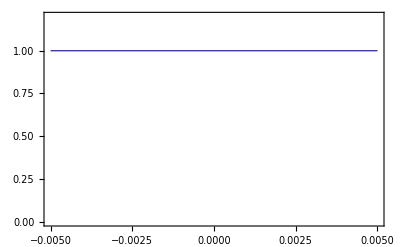

```mathematica
Clear[zed]
Plot[Evaluate[{Ng0[zed]+Ng1[zed]+Ng2a[zed]+Ng2b[zed]+Ne0[zed]+Ne1[zed]+Ne2a[zed]+Ne2b[zed]+v1Ng0[zed]+v1Ng1[zed]+v1Ng2a[zed]+v1Ng2b[zed]+jNg0[zed]+jNg0a[zed]+jNg0b[zed]+jNg1[zed]+jNg2a[zed]+jNg2b[zed]+jNg3a[zed]+jNg3b[zed]+v1jNg0[zed]+v1jNg0a[zed]+v1jNg0b[zed]+v1jNg1[zed]+v1jNg2a[zed]+v1jNg2b[zed]+v1jNg3a[zed]+v1jNg3b[zed]+v2Ng0[zed]+v2Ng1[zed]+v2Ng2a[zed]+v2Ng2b[zed]+v1Ne0[zed]+v1Ne1[zed]+v1Ne2a[zed]+v1Ne2b[zed]+v2jNg0[zed]+v2jNg0a[zed]+v2jNg0b[zed]+v2jNg1[zed]+v2jNg2a[zed]+v2jNg2b[zed]+v2jNg3a[zed]+v2jNg3b[zed]}/.sol],{zed,-ini,ini},PlotRange->{0,1.2},Frame->True,Axes->None,LabelStyle->Directive[Medium]]
```

```mathematica
Export["totalpopulation.png",%,ImageResolution->400]
```

totalpopulation.png

## Simulated signals

ListPlot::lpn: {{}} is not a list of numbers or pairs of numbers.

ListPlot[{},PlotRange→All]

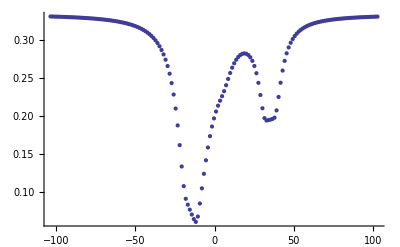

```mathematica
signal={};
signal2={}; (*here it solves the above coupled equations for laser detunings plus/minus 100 MHz in steps of 1 MHz*)
For [i=-650,i<651,i=i+8,
δ=i*10^6;
sol=NDSolve[
{v*Ng0'[z]==s12*R[δ,z]*(Ne2a[z]+Ne2b[z]-2Ng0[z])+(x00/8)*Γ*(Ne1[z]+Ne2a[z]+Ne2b[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+v1Ne2b[z]),
v*Ng1'[z]==s12*R[δ+Δg12,z]*(Ne2a[z]+Ne2b[z]-2Ng1[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*Ng2a'[z]==s12*R[δ+Δg12,z]*(Ne1[z]-Ng2a[z])+s12*R[δ+Δg12-Δe,z]*(Ne0[z]-Ng2a[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2a[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2a[z]),v*Ng2b'[z]==s12*R[δ+Δg12,z]*(Ne1[z]-Ng2b[z])+s12*R[δ+Δg12-Δe,z]*(Ne0[z]-Ng2b[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2b[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2b[z]),

v*jNg0'[z]==s32*R[δ+Δg32,z]*(Ne2a[z]+Ne2b[z]-2*jNg0[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*jNg0a'[z]==s32*R[δ+Δg32,z]*(Ne1[z]-jNg0a[z])+s32*R[δ+Δg32-Δe,z]*(Ne0[z]-jNg0a[z])+(x00/8)*Γ*(Ne1[z]+Ne2a[z]+(8/6)*Ne0[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+(8/6)*v1Ne0[z]),
v*jNg0b'[z]==s32*R[δ+Δg32,z]*(Ne1[z]-jNg0b[z])+s32*R[δ+Δg32-Δe,z]*(Ne0[z]-jNg0b[z])+(x00/8)*Γ*(Ne1[z]+Ne2b[z]+(8/6)*Ne0[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2b[z]+(8/6)*v1Ne0[z]),
v*jNg1'[z]==s32*R[δ,z]*(Ne2a[z]+Ne2b[z]-2jNg1[z])+(x00/8)*Γ*(Ne2a[z]+Ne2b[z]+Ne1[z])+(r10/8)*Γ*(v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),
v*jNg2a'[z]==s32*R[δ,z]*(Ne1[z]+-jNg2a[z])+(x00/8)*Γ*(Ne1[z]+Ne2a[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2a[z]),
v*jNg2b'[z]==s32*R[δ,z]*(Ne1[z]+-jNg2b[z])+(x00/8)*Γ*(Ne1[z]+Ne2b[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2b[z]),
v*jNg3a'[z]==s32*R[δ,z]*(Ne2a[z]-jNg3a[z])+(x00/8)*Γ*(Ne2a[z])+(r10/8)*Γ*(v1Ne2a[z]),
v*jNg3b'[z]==s32*R[δ,z]*(Ne2b[z]-jNg3b[z])+(x00/8)*Γ*(Ne2b[z])+(r10/8)*Γ*(v1Ne2b[z]),

v*v1Ng0'[z]==s12*R01[δ,z]*(Ne2a[z]+Ne2b[z]-2v1Ng0[z])+(x01/8)*Γ*(Ne1[z]+Ne2a[z]+Ne2b[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v1Ng1'[z]==s12*R01[δ+Δg12,z]*(Ne2a[z]+Ne2b[z]-2v1Ng1[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v1Ng2a'[z]==s12*R01[δ+Δg12,z]*(Ne1[z]-v1Ng2a[z])+s12*R01[δ+Δg12-Δe,z]*(Ne0[z]-v1Ng2a[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2a[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2a[z]),v*v1Ng2b'[z]==s12*R01[δ+Δg12,z]*(Ne1[z]-v1Ng2b[z])+s12*R01[δ+Δg12-Δe,z]*(Ne0[z]-v1Ng2b[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2b[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2b[z]),

v*v1jNg0'[z]==s32*R01[δ+Δg32,z]*(Ne2a[z]+Ne2b[z]-2v1jNg0[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*v1jNg0a'[z]==s32*R01[δ+Δg32,z]*(Ne1[z]-v1jNg0a[z])+s32*R01[δ+Δg32-Δe,z]*(Ne0[z]-v1jNg0a[z])+(x01/8)*Γ*(Ne1[z]+Ne2a[z]+(8/6)*Ne0[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+(8/6)*v1Ne0[z]),
v*v1jNg0b'[z]==s32*R01[δ+Δg32,z]*(Ne1[z]-v1jNg0b[z])+s32*R01[δ+Δg32-Δe,z]*(Ne0[z]-v1jNg0b[z])+(x01/8)*Γ*(Ne1[z]+Ne2b[z]+(8/6)*Ne0[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2b[z]+(8/6)*v1Ne0[z]),
v*v1jNg1'[z]==s32*R01[δ,z]*(Ne2a[z]+Ne2b[z]-2v1jNg1[z])+(x01/8)*Γ*(Ne2a[z]+Ne2b[z]+Ne1[z])+(r11/8)*Γ*(v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),
v*v1jNg2a'[z]==s32*R01[δ,z]*(Ne1[z]-v1jNg2a[z])+(x01/8)*Γ*(Ne1[z]+Ne2a[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2a[z]),
v*v1jNg2b'[z]==s32*R01[δ,z]*(Ne1[z]-v1jNg2b[z])+(x01/8)*Γ*(Ne1[z]+Ne2b[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2b[z]),
v*v1jNg3a'[z]==s32*R01[δ,z]*(Ne2a[z]-v1jNg3a[z])+(x01/8)*Γ*(Ne2a[z])+(r11/8)*Γ*(v1Ne2a[z]),
v*v1jNg3b'[z]==s32*R01[δ,z]*(Ne2b[z]-v1jNg3b[z])+(x01/8)*Γ*(Ne2b[z])+(r11/8)*Γ*(v1Ne2b[z]),

v*v2Ng0'[z]==s12*R12[δ,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2Ng0[z])+(r02/8)*Γ*(Ne1[z]+Ne2a[z]+Ne2b[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v2Ng1'[z]==s12*R12[δ+Δg12,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2Ng1[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v2Ng2a'[z]==s12*R12[δ+Δg12,z]*(v1Ne1[z]-v2Ng2a[z])+s12*R12[δ+Δg12-Δe,z]*(v1Ne0[z]-v2Ng2a[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2a[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2a[z]),v*v2Ng2b'[z]==s12*R12[δ+Δg12,z]*(v1Ne1[z]-v2Ng2b[z])+s12*R12[δ+Δg12-Δe,z]*(v1Ne0[z]-v2Ng2b[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2b[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2b[z]),

v*v2jNg0'[z]==s32*R12[δ+Δg32,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2jNg0[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*v2jNg0a'[z]==s32*R12[δ+Δg32,z]*(v1Ne1[z]-v2jNg0a[z])+s32*R12[δ+Δg32-Δe,z]*(v1Ne0[z]-v2jNg0a[z])+(r02/8)*Γ*(Ne1[z]+Ne2a[z]+(8/6)*Ne0[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+(8/6)*v1Ne0[z]),
v*v2jNg0b'[z]==s32*R12[δ+Δg32,z]*(v1Ne1[z]-v2jNg0b[z])+s32*R12[δ+Δg32-Δe,z]*(v1Ne0[z]-v2jNg0b[z])+(r02/8)*Γ*(Ne1[z]+Ne2b[z]+(8/6)*Ne0[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2b[z]+(8/6)*v1Ne0[z]),
v*v2jNg1'[z]==s32*R12[δ,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2jNg1[z])+(r02/8)*Γ*(Ne2a[z]+Ne2b[z]+Ne1[z])+(r12/8)*Γ*(v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),
v*v2jNg2a'[z]==s32*R12[δ,z]*(v1Ne1[z]-v2jNg2a[z])+(r02/8)*Γ*(Ne1[z]+Ne2a[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2a[z]),
v*v2jNg2b'[z]==s32*R12[δ,z]*(v1Ne1[z]-v2jNg2b[z])+(r02/8)*Γ*(Ne1[z]+Ne2b[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2b[z]),
v*v2jNg3a'[z]==s32*R12[δ,z]*(v1Ne2a[z]-v2jNg3a[z])+(r02/8)*Γ*(Ne2a[z])+(r12/8)*Γ*(v1Ne2a[z]),
v*v2jNg3b'[z]==s32*R12[δ,z]*(v1Ne2b[z]-v2jNg3b[z])+(r02/8)*Γ*(Ne2b[z])+(r12/8)*Γ*(v1Ne2b[z]),

v*Ne0'[z]==s12*R[δ+Δg12-Δe,z]*(Ng2a[z]+Ng2b[z]-2Ne0[z])+s32*R[δ+Δg32-Δe,z]*(jNg0a[z]+jNg0b[z]-2Ne0[z])+s12*R01[δ+Δg12-Δe,z]*(v1Ng2a[z]+v1Ng2b[z]-2Ne0[z])+s32*R01[δ+Δg32-Δe,z]*(v1jNg0a[z]+v1jNg0b[z]-2Ne0[z])-Γ*(Ne0[z]),
v*Ne1'[z]==s32*R[δ+Δg32,z]*(jNg0a[z]+jNg0b[z]-2Ne1[z])+s12*R[δ+Δg12,z]*(Ng2a[z]+Ng2b[z]-2Ne1[z])+s32*R[δ,z]*(jNg2a[z]+jNg2b[z]-2Ne1[z])+s12*R01[δ+Δg12,z]*(v1Ng2a[z]+v1Ng2b[z]-2Ne1[z])+s32*R01[δ+Δg32,z]*(v1jNg0a[z]+v1jNg0b[z]-2Ne1[z])+s32*R01[δ,z]*(v1jNg2a[z]+v1jNg2b[z]-2Ne1[z])-Γ*(Ne1[z]),
v*Ne2a'[z]==s12*R[δ+Δg12,z]*(Ng1[z]-Ne2a[z])+s32*R[δ+Δg32,z]*(jNg0[z]-Ne2a[z])+s12*R[δ,z]*(Ng0[z]-Ne2a[z])+s32*R[δ,z]*(jNg1[z]+jNg3a[z]-2Ne2a[z])+s12*R01[δ+Δg12,z]*(v1Ng1[z]-Ne2a[z])+s32*R01[δ+Δg32,z]*(v1jNg0[z]-Ne2a[z])+s12*R01[δ,z]*(v1Ng0[z]-Ne2a[z])+s32*R01[δ,z]*(v1jNg1[z]+v1jNg3a[z]-2Ne2a[z])-Γ*Ne2a[z],
v*Ne2b'[z]==s12*R[δ+Δg12,z]*(Ng1[z]-Ne2b[z])+s32*R[δ+Δg32,z]*(jNg0[z]-Ne2b[z])+s12*R[δ,z]*(Ng0[z]-Ne2b[z])+s32*R[δ,z]*(jNg1[z]+jNg3b[z]-2Ne2b[z])+s12*R01[δ+Δg12,z]*(v1Ng1[z]-Ne2b[z])+s32*R01[δ+Δg32,z]*(v1jNg0[z]-Ne2b[z])+s12*R01[δ,z]*(v1Ng0[z]-Ne2b[z])+s32*R01[δ,z]*(v1jNg1[z]+v1jNg3b[z]-2Ne2b[z])-Γ*Ne2b[z],

v*v1Ne0'[z]==s12*R12[δ+Δg12-Δe,z]*(v2Ng2a[z]+v2Ng2b[z]-2v1Ne0[z])+s32*R12[δ+Δg32-Δe,z]*(v2jNg0a[z]+v2jNg0b[z]-2v1Ne0[z])-Γ*(v1Ne0[z]),
v*v1Ne1'[z]==s12*R12[δ+Δg12,z]*(v2Ng2a[z]+v2Ng2b[z]-2v1Ne1[z])+s32*R12[δ+Δg32,z]*(v2jNg0a[z]+v2jNg0b[z]-2v1Ne1[z])+R12[δ,z]*(v2jNg2a[z]+v2jNg2b[z]-2v1Ne1[z])-Γ*(v1Ne1[z]),
v*v1Ne2a'[z]==s12*R12[δ+Δg12,z]*(v2Ng1[z]-v1Ne2a[z])+s32*R12[δ+Δg32,z]*(v2jNg0[z]-v1Ne2a[z])+s12*R12[δ,z]*(v2Ng0[z]-v1Ne2a[z])+s32*R12[δ,z]*(v2jNg1[z]+v2jNg3a[z]-2v1Ne2a[z])-Γ*v1Ne2a[z],
v*v1Ne2b'[z]==s12*R12[δ+Δg12,z]*(v2Ng1[z]-v1Ne2b[z])+s32*R12[δ+Δg32,z]*(v2jNg0[z]-v1Ne2b[z])+s12*R12[δ,z]*(v2Ng0[z]-v1Ne2b[z])+s32*R12[δ,z]*(v2jNg1[z]+v2jNg3b[z]-2v1Ne2b[z])-Γ*v1Ne2b[z],

v*lost'[z]==(r03)*Γ*(Ne0[z]+Ne2a[z]+Ne2b[z]+Ne1[z])+(r13)*Γ*(v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),

Ng0[ini]==1/ns,Ng1[ini]==1/ns,Ng2a[ini]==1/ns,Ng2b[ini]==1/ns,Ne0[ini]==0,Ne1[ini]==0,Ne2a[ini]==0,Ne2b[ini]==0,v1Ne0[ini]==0,v1Ne1[ini]==0,v1Ne2a[ini]==0,v1Ne2b[ini]==0,v1Ng0[ini]==0,v1Ng1[ini]==0,v1Ng2a[ini]==0,v1Ng2b[ini]==0,jNg0[ini]==1/ns,jNg0a[ini]==1/ns,jNg0b[ini]==1/ns,jNg1[ini]==1/ns,jNg2a[ini]==1/ns,jNg2b[ini]==1/ns,jNg3a[ini]==1/ns,jNg3b[ini]==1/ns,v1jNg0[ini]==0,v1jNg0a[ini]==0,v1jNg0b[ini]==0,v1jNg1[ini]==0,v1jNg2a[ini]==0,v1jNg2b[ini]==0,v1jNg3a[ini]==0,v1jNg3b[ini]==0,v2Ng0[ini]==0,v2Ng1[ini]==0,v2Ng2a[ini]==0,v2Ng2b[ini]==0,v2jNg0[ini]==0,v2jNg0a[ini]==0,v2jNg0b[ini]==0,v2jNg1[ini]==0,v2jNg2a[ini]==0,v2jNg2b[ini]==0,v2jNg3a[ini]==0,v2jNg3b[ini]==0,lost[ini]==0},

{Ng0,Ng1,Ng2a,Ng2b,Ne0,Ne1,Ne2a,Ne2b,v1Ne0,v1Ne1,v1Ne2a,v1Ne2b,v1Ng0,v1Ng1,v1Ng2a,v1Ng2b,jNg0,jNg0a,jNg0b,jNg1,jNg2a,jNg2b,jNg3a,jNg3b,v1jNg0,v1jNg0a,v1jNg0b,v1jNg1,v1jNg2a,v1jNg2b,v1jNg3a,v1jNg3b,v2Ng0,v2Ng1,v2Ng2a,v2Ng2b,v2jNg0,v2jNg0a,v2jNg0b,v2jNg1,v2jNg2a,v2jNg2b,v2jNg3a,v2jNg3b,lost},{z,ini,-ini}];

(*molec= (NIntegrate[Evaluate[{Ne0[z],Ne1[z],Ne2a[z],Ne2b[z],v1Ne0[z],v1Ne1[z],v1Ne2a[z],v1Ne2b[z]}/.sol],{z,ini, -ini}])*Γ/v;
m=Total[molec[[1]]];
signal=Append[signal,{δ/(2*Pi*10^6),m}];*)
zed=0.004;
molNo=Evaluate[{Ng0[zed]+Ng1[zed]+Ng2a[zed]+Ng2b[zed]}/.sol][[1]];
signal2=Append[signal2,{δ/(2*Pi*10^6),molNo[[1]]}];
]
ListPlot[signal,PlotRange->All]
ListPlot[signal2,PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
zed=0.004;
molNo=Evaluate[{Ng0[zed]+Ng1[zed]+Ng2a[zed]+Ng2b[zed]}/.sol][[1]]
```

{0.0619841}

```mathematica
ListPlot[signal2,PlotRange->All, AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
signal2[[1]]
```

{-325/π,0.330416}

## Saturation Intensity Curves

```mathematica
lis={};
mono={};
For [i=0.001,i <5,
I0=i*Isat;(*probe laser intensity*)
I01=00*Isat01;(*probe laser intensity*)
I12=0*Isat12;
power00=I0*Pi*0.001^2;
power01=I01*Pi*0.005^2;
power12=I12*Pi*0.005^2;
δ=-15*10^6;(*probe laser detuning*)
R[δ_,z_]:=((Γ/2)/(1+4δ^2/Γ^2))*((I0*(Tanh[z/d+L/d]-Tanh[z/d-L/d])/(2Tanh[L/d]))/Isat);(* excitation rate00*)
sol=NDSolve[
{v*Ng0'[z]==s12*R[δ,z]*(Ne2a[z]+Ne2b[z]-2Ng0[z])+(x00/8)*Γ*(Ne1[z]+Ne2a[z]+Ne2b[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+v1Ne2b[z]),
v*Ng1'[z]==s12*R[δ+Δg12,z]*(Ne2a[z]+Ne2b[z]-2Ng1[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*Ng2a'[z]==s12*R[δ+Δg12,z]*(Ne1[z]-Ng2a[z])+s12*R[δ+Δg12-Δe,z]*(Ne0[z]-Ng2a[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2a[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2a[z]),v*Ng2b'[z]==s12*R[δ+Δg12,z]*(Ne1[z]-Ng2b[z])+s12*R[δ+Δg12-Δe,z]*(Ne0[z]-Ng2b[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2b[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2b[z]),

v*jNg0'[z]==s32*R[δ+Δg32,z]*(Ne2a[z]+Ne2b[z]-2*jNg0[z])+(x00/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r10/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*jNg0a'[z]==s32*R[δ+Δg32,z]*(Ne1[z]-jNg0a[z])+s32*R[δ+Δg32-Δe,z]*(Ne0[z]-jNg0a[z])+(x00/8)*Γ*(Ne1[z]+Ne2a[z]+(8/6)*Ne0[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+(8/6)*v1Ne0[z]),
v*jNg0b'[z]==s32*R[δ+Δg32,z]*(Ne1[z]-jNg0b[z])+s32*R[δ+Δg32-Δe,z]*(Ne0[z]-jNg0b[z])+(x00/8)*Γ*(Ne1[z]+Ne2b[z]+(8/6)*Ne0[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2b[z]+(8/6)*v1Ne0[z]),
v*jNg1'[z]==s32*R[δ,z]*(Ne2a[z]+Ne2b[z]-2jNg1[z])+(x00/8)*Γ*(Ne2a[z]+Ne2b[z]+Ne1[z])+(r10/8)*Γ*(v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),
v*jNg2a'[z]==s32*R[δ,z]*(Ne1[z]+-jNg2a[z])+(x00/8)*Γ*(Ne1[z]+Ne2a[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2a[z]),
v*jNg2b'[z]==s32*R[δ,z]*(Ne1[z]+-jNg2b[z])+(x00/8)*Γ*(Ne1[z]+Ne2b[z])+(r10/8)*Γ*(v1Ne1[z]+v1Ne2b[z]),
v*jNg3a'[z]==s32*R[δ,z]*(Ne2a[z]-jNg3a[z])+(x00/8)*Γ*(Ne2a[z])+(r10/8)*Γ*(v1Ne2a[z]),
v*jNg3b'[z]==s32*R[δ,z]*(Ne2b[z]-jNg3b[z])+(x00/8)*Γ*(Ne2b[z])+(r10/8)*Γ*(v1Ne2b[z]),

v*v1Ng0'[z]==s12*R01[δ,z]*(Ne2a[z]+Ne2b[z]-2v1Ng0[z])+(x01/8)*Γ*(Ne1[z]+Ne2a[z]+Ne2b[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v1Ng1'[z]==s12*R01[δ+Δg12,z]*(Ne2a[z]+Ne2b[z]-2v1Ng1[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v1Ng2a'[z]==s12*R01[δ+Δg12,z]*(Ne1[z]-v1Ng2a[z])+s12*R01[δ+Δg12-Δe,z]*(Ne0[z]-v1Ng2a[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2a[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2a[z]),v*v1Ng2b'[z]==s12*R01[δ+Δg12,z]*(Ne1[z]-v1Ng2b[z])+s12*R01[δ+Δg12-Δe,z]*(Ne0[z]-v1Ng2b[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2b[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2b[z]),

v*v1jNg0'[z]==s32*R01[δ+Δg32,z]*(Ne2a[z]+Ne2b[z]-2v1jNg0[z])+(x01/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r11/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*v1jNg0a'[z]==s32*R01[δ+Δg32,z]*(Ne1[z]-v1jNg0a[z])+s32*R01[δ+Δg32-Δe,z]*(Ne0[z]-v1jNg0a[z])+(x01/8)*Γ*(Ne1[z]+Ne2a[z]+(8/6)*Ne0[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+(8/6)*v1Ne0[z]),
v*v1jNg0b'[z]==s32*R01[δ+Δg32,z]*(Ne1[z]-v1jNg0b[z])+s32*R01[δ+Δg32-Δe,z]*(Ne0[z]-v1jNg0b[z])+(x01/8)*Γ*(Ne1[z]+Ne2b[z]+(8/6)*Ne0[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2b[z]+(8/6)*v1Ne0[z]),
v*v1jNg1'[z]==s32*R01[δ,z]*(Ne2a[z]+Ne2b[z]-2v1jNg1[z])+(x01/8)*Γ*(Ne2a[z]+Ne2b[z]+Ne1[z])+(r11/8)*Γ*(v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),
v*v1jNg2a'[z]==s32*R01[δ,z]*(Ne1[z]-v1jNg2a[z])+(x01/8)*Γ*(Ne1[z]+Ne2a[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2a[z]),
v*v1jNg2b'[z]==s32*R01[δ,z]*(Ne1[z]-v1jNg2b[z])+(x01/8)*Γ*(Ne1[z]+Ne2b[z])+(r11/8)*Γ*(v1Ne1[z]+v1Ne2b[z]),
v*v1jNg3a'[z]==s32*R01[δ,z]*(Ne2a[z]-v1jNg3a[z])+(x01/8)*Γ*(Ne2a[z])+(r11/8)*Γ*(v1Ne2a[z]),
v*v1jNg3b'[z]==s32*R01[δ,z]*(Ne2b[z]-v1jNg3b[z])+(x01/8)*Γ*(Ne2b[z])+(r11/8)*Γ*(v1Ne2b[z]),

v*v2Ng0'[z]==s12*R12[δ,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2Ng0[z])+(r02/8)*Γ*(Ne1[z]+Ne2a[z]+Ne2b[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v2Ng1'[z]==s12*R12[δ+Δg12,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2Ng1[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),
v*v2Ng2a'[z]==s12*R12[δ+Δg12,z]*(v1Ne1[z]-v2Ng2a[z])+s12*R12[δ+Δg12-Δe,z]*(v1Ne0[z]-v2Ng2a[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2a[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2a[z]),v*v2Ng2b'[z]==s12*R12[δ+Δg12,z]*(v1Ne1[z]-v2Ng2b[z])+s12*R12[δ+Δg12-Δe,z]*(v1Ne0[z]-v2Ng2b[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne1[z]+Ne2b[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne1[z]+v1Ne2b[z]),

v*v2jNg0'[z]==s32*R12[δ+Δg32,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2jNg0[z])+(r02/8)*Γ*((8/6)*Ne0[z]+Ne2a[z]+Ne2b[z])+(r12/8)*Γ*((8/6)*v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]),v*v2jNg0a'[z]==s32*R12[δ+Δg32,z]*(v1Ne1[z]-v2jNg0a[z])+s32*R12[δ+Δg32-Δe,z]*(v1Ne0[z]-v2jNg0a[z])+(r02/8)*Γ*(Ne1[z]+Ne2a[z]+(8/6)*Ne0[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2a[z]+(8/6)*v1Ne0[z]),
v*v2jNg0b'[z]==s32*R12[δ+Δg32,z]*(v1Ne1[z]-v2jNg0b[z])+s32*R12[δ+Δg32-Δe,z]*(v1Ne0[z]-v2jNg0b[z])+(r02/8)*Γ*(Ne1[z]+Ne2b[z]+(8/6)*Ne0[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2b[z]+(8/6)*v1Ne0[z]),
v*v2jNg1'[z]==s32*R12[δ,z]*(v1Ne2a[z]+v1Ne2b[z]-2v2jNg1[z])+(r02/8)*Γ*(Ne2a[z]+Ne2b[z]+Ne1[z])+(r12/8)*Γ*(v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),
v*v2jNg2a'[z]==s32*R12[δ,z]*(v1Ne1[z]-v2jNg2a[z])+(r02/8)*Γ*(Ne1[z]+Ne2a[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2a[z]),
v*v2jNg2b'[z]==s32*R12[δ,z]*(v1Ne1[z]-v2jNg2b[z])+(r02/8)*Γ*(Ne1[z]+Ne2b[z])+(r12/8)*Γ*(v1Ne1[z]+v1Ne2b[z]),
v*v2jNg3a'[z]==s32*R12[δ,z]*(v1Ne2a[z]-v2jNg3a[z])+(r02/8)*Γ*(Ne2a[z])+(r12/8)*Γ*(v1Ne2a[z]),
v*v2jNg3b'[z]==s32*R12[δ,z]*(v1Ne2b[z]-v2jNg3b[z])+(r02/8)*Γ*(Ne2b[z])+(r12/8)*Γ*(v1Ne2b[z]),

v*Ne0'[z]==s12*R[δ+Δg12-Δe,z]*(Ng2a[z]+Ng2b[z]-2Ne0[z])+s32*R[δ+Δg32-Δe,z]*(jNg0a[z]+jNg0b[z]-2Ne0[z])+s12*R01[δ+Δg12-Δe,z]*(v1Ng2a[z]+v1Ng2b[z]-2Ne0[z])+s32*R01[δ+Δg32-Δe,z]*(v1jNg0a[z]+v1jNg0b[z]-2Ne0[z])-Γ*(Ne0[z]),
v*Ne1'[z]==s32*R[δ+Δg32,z]*(jNg0a[z]+jNg0b[z]-2Ne1[z])+s12*R[δ+Δg12,z]*(Ng2a[z]+Ng2b[z]-2Ne1[z])+s32*R[δ,z]*(jNg2a[z]+jNg2b[z]-2Ne1[z])+s12*R01[δ+Δg12,z]*(v1Ng2a[z]+v1Ng2b[z]-2Ne1[z])+s32*R01[δ+Δg32,z]*(v1jNg0a[z]+v1jNg0b[z]-2Ne1[z])+s32*R01[δ,z]*(v1jNg2a[z]+v1jNg2b[z]-2Ne1[z])-Γ*(Ne1[z]),
v*Ne2a'[z]==s12*R[δ+Δg12,z]*(Ng1[z]-Ne2a[z])+s32*R[δ+Δg32,z]*(jNg0[z]-Ne2a[z])+s12*R[δ,z]*(Ng0[z]-Ne2a[z])+s32*R[δ,z]*(jNg1[z]+jNg3a[z]-2Ne2a[z])+s12*R01[δ+Δg12,z]*(v1Ng1[z]-Ne2a[z])+s32*R01[δ+Δg32,z]*(v1jNg0[z]-Ne2a[z])+s12*R01[δ,z]*(v1Ng0[z]-Ne2a[z])+s32*R01[δ,z]*(v1jNg1[z]+v1jNg3a[z]-2Ne2a[z])-Γ*Ne2a[z],
v*Ne2b'[z]==s12*R[δ+Δg12,z]*(Ng1[z]-Ne2b[z])+s32*R[δ+Δg32,z]*(jNg0[z]-Ne2b[z])+s12*R[δ,z]*(Ng0[z]-Ne2b[z])+s32*R[δ,z]*(jNg1[z]+jNg3b[z]-2Ne2b[z])+s12*R01[δ+Δg12,z]*(v1Ng1[z]-Ne2b[z])+s32*R01[δ+Δg32,z]*(v1jNg0[z]-Ne2b[z])+s12*R01[δ,z]*(v1Ng0[z]-Ne2b[z])+s32*R01[δ,z]*(v1jNg1[z]+v1jNg3b[z]-2Ne2b[z])-Γ*Ne2b[z],

v*v1Ne0'[z]==s12*R12[δ+Δg12-Δe,z]*(v2Ng2a[z]+v2Ng2b[z]-2v1Ne0[z])+s32*R12[δ+Δg32-Δe,z]*(v2jNg0a[z]+v2jNg0b[z]-2v1Ne0[z])-Γ*(v1Ne0[z]),
v*v1Ne1'[z]==s12*R12[δ+Δg12,z]*(v2Ng2a[z]+v2Ng2b[z]-2v1Ne1[z])+s32*R12[δ+Δg32,z]*(v2jNg0a[z]+v2jNg0b[z]-2v1Ne1[z])+R12[δ,z]*(v2jNg2a[z]+v2jNg2b[z]-2v1Ne1[z])-Γ*(v1Ne1[z]),
v*v1Ne2a'[z]==s12*R12[δ+Δg12,z]*(v2Ng1[z]-v1Ne2a[z])+s32*R12[δ+Δg32,z]*(v2jNg0[z]-v1Ne2a[z])+s12*R12[δ,z]*(v2Ng0[z]-v1Ne2a[z])+s32*R12[δ,z]*(v2jNg1[z]+v2jNg3a[z]-2v1Ne2a[z])-Γ*v1Ne2a[z],
v*v1Ne2b'[z]==s12*R12[δ+Δg12,z]*(v2Ng1[z]-v1Ne2b[z])+s32*R12[δ+Δg32,z]*(v2jNg0[z]-v1Ne2b[z])+s12*R12[δ,z]*(v2Ng0[z]-v1Ne2b[z])+s32*R12[δ,z]*(v2jNg1[z]+v2jNg3b[z]-2v1Ne2b[z])-Γ*v1Ne2b[z],

v*lost'[z]==(r03)*Γ*(Ne0[z]+Ne2a[z]+Ne2b[z]+Ne1[z])+(r13)*Γ*(v1Ne0[z]+v1Ne2a[z]+v1Ne2b[z]+v1Ne1[z]),

Ng0[ini]==1/ns,Ng1[ini]==1/ns,Ng2a[ini]==1/ns,Ng2b[ini]==1/ns,Ne0[ini]==0,Ne1[ini]==0,Ne2a[ini]==0,Ne2b[ini]==0,v1Ne0[ini]==0,v1Ne1[ini]==0,v1Ne2a[ini]==0,v1Ne2b[ini]==0,v1Ng0[ini]==0,v1Ng1[ini]==0,v1Ng2a[ini]==0,v1Ng2b[ini]==0,jNg0[ini]==1/ns,jNg0a[ini]==1/ns,jNg0b[ini]==1/ns,jNg1[ini]==1/ns,jNg2a[ini]==1/ns,jNg2b[ini]==1/ns,jNg3a[ini]==1/ns,jNg3b[ini]==1/ns,v1jNg0[ini]==0,v1jNg0a[ini]==0,v1jNg0b[ini]==0,v1jNg1[ini]==0,v1jNg2a[ini]==0,v1jNg2b[ini]==0,v1jNg3a[ini]==0,v1jNg3b[ini]==0,v2Ng0[ini]==0,v2Ng1[ini]==0,v2Ng2a[ini]==0,v2Ng2b[ini]==0,v2jNg0[ini]==0,v2jNg0a[ini]==0,v2jNg0b[ini]==0,v2jNg1[ini]==0,v2jNg2a[ini]==0,v2jNg2b[ini]==0,v2jNg3a[ini]==0,v2jNg3b[ini]==0,lost[ini]==0},

{Ng0,Ng1,Ng2a,Ng2b,Ne0,Ne1,Ne2a,Ne2b,v1Ne0,v1Ne1,v1Ne2a,v1Ne2b,v1Ng0,v1Ng1,v1Ng2a,v1Ng2b,jNg0,jNg0a,jNg0b,jNg1,jNg2a,jNg2b,jNg3a,jNg3b,v1jNg0,v1jNg0a,v1jNg0b,v1jNg1,v1jNg2a,v1jNg2b,v1jNg3a,v1jNg3b,v2Ng0,v2Ng1,v2Ng2a,v2Ng2b,v2jNg0,v2jNg0a,v2jNg0b,v2jNg1,v2jNg2a,v2jNg2b,v2jNg3a,v2jNg3b,lost},{z,ini,-ini}];

zed=0.004;
gndmolNo=Evaluate[{Ng0[zed]+Ng1[zed]+Ng2a[zed]+Ng2b[zed]}/.sol][[1]];
(*signal2=Append[signal2,{δ/(2*Pi*10^6),gndmolNo[[1]]}];*)
(*Exphotons=(NIntegrate[Evaluate[{Ne0[z],Ne1[z],Ne2a[z],Ne2b[z],v1Ne0[z],v1Ne1[z],v1Ne2a[z],v1Ne2b[z]}/.sol],{z,ini,-ini}])*Γ/v ;
signal=Total[Exphotons[[1]]]; (*Integrated signal*)*)
lis=Append[lis,{power00*1000,(0.33-gndmolNo[[1]])/0.33}];
moleculeNo=Evaluate[{Ng0[zed]+Ng1[zed]+Ng2a[zed]+Ng2b[zed]+Ne0[zed]+Ne1[zed]+Ne2a[zed]+Ne2b[zed]+v1Ng0[zed]+v1Ng1[zed]+v1Ng2a[zed]+v1Ng2b[zed]+jNg0[zed]+jNg0a[zed]+jNg0b[zed]+jNg1[zed]+jNg2a[zed]+jNg2b[zed]+jNg3a[zed]+jNg3b[zed]+v1jNg0[zed]+v1jNg0a[zed]+v1jNg0b[zed]+v1jNg1[zed]+v1jNg2a[zed]+v1jNg2b[zed]+v1jNg3a[zed]+v1jNg3b[zed]+v2Ng0[zed]+v2Ng1[zed]+v2Ng2a[zed]+v2Ng2b[zed]+v1Ne0[zed]+v1Ne1[zed]+v1Ne2a[zed]+v1Ne2b[zed]+v2jNg0[zed]+v2jNg0a[zed]+v2jNg0b[zed]+v2jNg1[zed]+v2jNg2a[zed]+v2jNg2b[zed]+v2jNg3a[zed]+v2jNg3b[zed]}/.sol];
mono=Append[mono,{power00*1000,moleculeNo[[1]][[1]]}];
i=i*1.1;
]
```

## Ground state population(Depletion signal) at BSigma peak as a function of 905 power

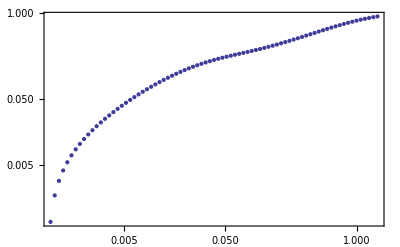

```mathematica
ListLogLogPlot[lis,PlotRange->All,Frame->True,Axes->None,LabelStyle->Directive[Medium]]
```

```mathematica
Export["gndpopvs12power.png",%,ImageResolution->500]
```

gndpopvs12power.png

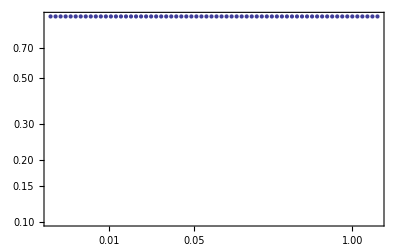

```mathematica
ListLogLogPlot[mono,PlotRange->{0.1,1},Frame->True,Axes->None,LabelStyle->Directive[Medium]]
```

```mathematica
Varying R01 laser power (mW), R00 power fixed to 20 mW
```

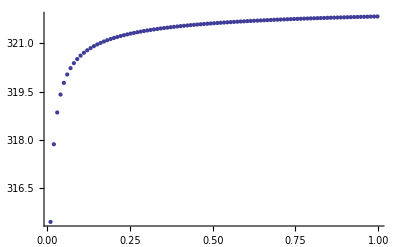

```mathematica
ListPlot[lis,PlotRange->All]
```

```mathematica
m=139*1.66*10^(-27);
m*v^2*(1/2)*λ/(h*c)
```

0.0118263

```mathematica
m*v^2*(1/2)
```

2.59583×10^-21

```mathematica
(λ*m*80/h)
```

25211.9

```mathematica
150/0.01
```

15000.

```mathematica
2*Pi/(100.*10^(-9))
```

6.28319×10^7

```mathematica
r11+r10+r12+0.00071
```

1.

```mathematica
r01+r00+r02
```

0.99997

```mathematica
Length[{Ng0,Ng1,Ng2a,Ng2b,Ne0,Ne1,Ne2a,Ne2b,v1Ne0,v1Ne1,v1Ne2a,v1Ne2b,v1Ng0,v1Ng1,v1Ng2a,v1Ng2b,jNg0,jNg0a,jNg0b,jNg1,jNg2a,jNg2b,jNg3a,jNg3b,v1jNg0,v1jNg0a,v1jNg0b,v1jNg1,v1jNg2a,v1jNg2b,v1jNg3a,v1jNg3b,v2Ng0,v2Ng1,v2Ng2a,v2Ng2b,v2jNg0,v2jNg0a,v2jNg0b,v2jNg1,v2jNg2a,v2jNg2b,v2jNg3a,v2jNg3b,lost}]
```

45